```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
Estrai[filename_,histo_,namehisto_,nhisto_]:=Module[{file,positions,binning},
histo=.;
namehisto=.;
nhisto=.;
file=Import[filename,"Table"];
nhisto=0;
namehisto=Table[0,{j,1,100}];
positions=Table[0,{j,1,100}];
Do[
If[file[[i]]=={"<Histo>"}, 
nhisto=nhisto+1;
namehisto[[nhisto]]=file[[i+2]];
positions[[nhisto]]=i];
     ,{i,1,Length[file]}];
namehisto=Take[namehisto,nhisto];
positions=Take[positions,nhisto];
Do[(*Print[file[[ positions[[i]]+4 ]] ];*)binning[i]=file[[ positions[[i]]+4 ]];passo[i]=(binning[i][[3]]-binning[i][[2]])/binning[i][[1]],{i,1,nhisto}];
 Do[histo[i]=Table[{binning[i][[2]]+(j-1)passo[i],file[[positions[[i]]+18+j ,1 ]]},{j,0,binning[i][[1]]+1}],{i,1,nhisto}]
]
```

M(nunu)>500 GeV

```mathematica
(*namerun="Mnunu300"*)
namerun="Mnunu500"
```

Mnunu500

```mathematica
namefolder="mupem_to_mupemvtatvta_2to4";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etal=prova[5];
Mll =prova[14];
Mnn =prova[15];
etan=prova[10];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_PT},{10_ETA},{11_PT},{12_PT},{13_ETA},{14_M},{15_M},{16_M},{17_M},{18_M},{19_M},{20_DELTAR},{21_DELTAR},{22_MT_MET},{23_MT_MET}}

```mathematica
namefolder="mupem_to_mupemvtatvta_2to4_noQED";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalnoQED=prova[5];
MllnoQED =prova[14];
MnnnoQED =prova[15];
etannoQED=prova[10];
```

```mathematica
(*namerun="test180"*)
```

```mathematica
namefolder="ZZ_vtatvta_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZ =prova[10];
etanZZ=prova[6];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZmuhalf =prova[10];
etanZZmuhalf=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZmuquarter =prova[10];
etanZZmuquarter=prova[6];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZptmu =prova[10];
etanZZptmu=prova[6];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlegend={"2to4_noQED","2to4","ZZ Eva mu=sqrtshat","ZZ Eva mu=sqrtshat/2","ZZ Eva mu=sqrtshat/4","ZZ Eva mu=sqrtshat, pt evol"};
plotstyle={Thick,Thick,Dashed,Dashed,Dashed,Dashed}
plotlabel="e+ e- > nu_tau nu_tau~ at 10 TeV";
```

{Thickness[Large],Thickness[Large],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}]}

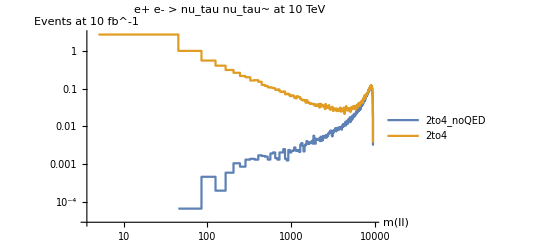

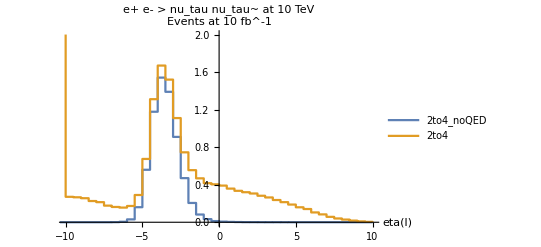

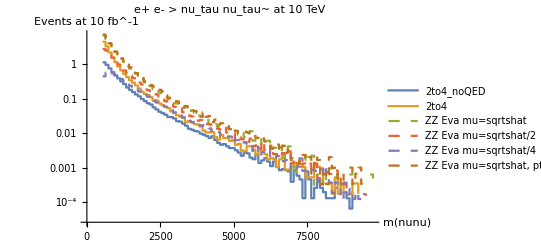

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

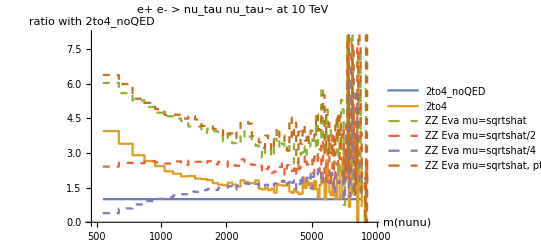

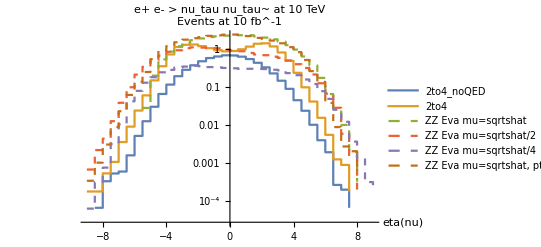

```mathematica
ListLogLogPlot[{joinbin[MllnoQED,4],joinbin[Mll,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListPlot[{joinbin[etalnoQED,1],joinbin[etal,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotRange->{{-10,10},{0,2}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[MnnnoQED,10],joinbin[Mnn,10],joinbin[MnnZZ,10],joinbin[MnnZZmuhalf,10],joinbin[MnnZZmuquarter,10],joinbin[MnnZZptmu,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","Events at 10 fb^-1"}] 

ListLogLinearPlot[{rapp[joinbin[MnnnoQED,10],joinbin[MnnnoQED,10]],rapp[joinbin[Mnn,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZ,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZmuhalf,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZmuquarter,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZptmu,10],joinbin[MnnnoQED,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","ratio with 2to4_noQED"}] 

ListLogPlot[{etannoQED,etan,etanZZ,etanZZmuhalf,etanZZmuquarter,etanZZptmu},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(nu)","Events at 10 fb^-1"}]
```

```mathematica
Plus@@Map[#[[2]]&,etan]
Plus@@Map[#[[2]]&,Mll]
Plus@@Map[#[[2]]&,Mnn]
Plus@@Map[#[[2]]&,etanZZ]
```

17.7102

17.7102

17.7102

32.206

M(nunu)>500 GeV con anche Pt(nu)> 150 GeV

```mathematica
(*namerun="Mnunu300"*)
namerun="Mnunu500_ptnu150"
```

Mnunu500_ptnu150

```mathematica
namefolder="mupem_to_mupemvtatvta_2to4";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etal=prova[5];
Mll =prova[14];
Mnn =prova[15];
etan=prova[10];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_PT},{10_ETA},{11_PT},{12_PT},{13_ETA},{14_M},{15_M},{16_M},{17_M},{18_M},{19_M},{20_DELTAR},{21_DELTAR},{22_MT_MET},{23_MT_MET}}

```mathematica
namefolder="mupem_to_mupemvtatvta_2to4_noQED";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalnoQED=prova[5];
MllnoQED =prova[14];
MnnnoQED =prova[15];
etannoQED=prova[10];
```

```mathematica
(*namerun="test180"*)
```

```mathematica
namefolder="ZZ_vtatvta_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZ =prova[10];
etanZZ=prova[6];
```

```mathematica
(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZmuhalf =prova[10];
etanZZmuhalf=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZmuquarter =prova[10];
etanZZmuquarter=prova[6];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZptmu =prova[10];
etanZZptmu=prova[6];*)
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="e+ e- > nu_tau nu_tau~ at 10 TeV";
```

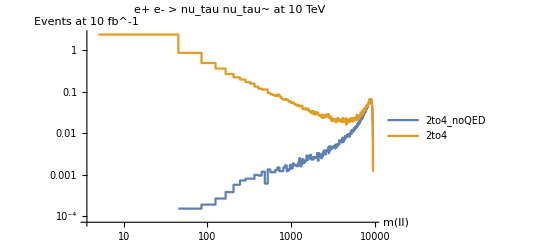

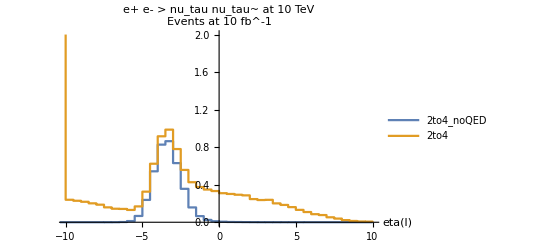

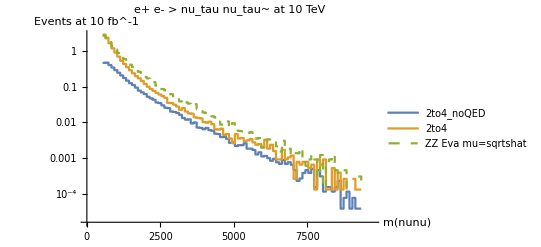

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

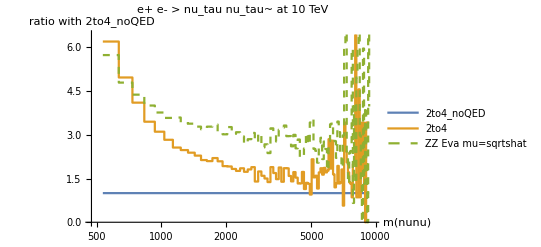

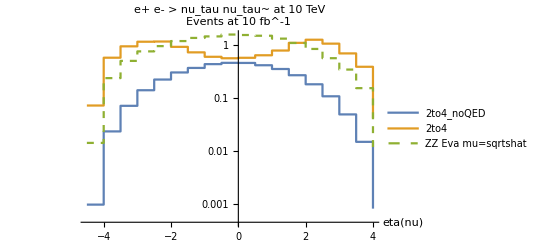

```mathematica
ListLogLogPlot[{joinbin[MllnoQED,4],joinbin[Mll,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListPlot[{joinbin[etalnoQED,1],joinbin[etal,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotRange->{{-10,10},{0,2}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[MnnnoQED,10],joinbin[Mnn,10],joinbin[MnnZZ,10](*,joinbin[MnnZZmuhalf,10],joinbin[MnnZZptmu,10]*)},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","Events at 10 fb^-1"}] 

ListLogLinearPlot[{rapp[joinbin[MnnnoQED,10],joinbin[MnnnoQED,10]],rapp[joinbin[Mnn,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZ,10],joinbin[MnnnoQED,10]](*,rapp[joinbin[MnnZZmuhalf,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZptmu,10],joinbin[MnnnoQED,10]]*)},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","ratio with 2to4_noQED"}] 

ListLogPlot[{etannoQED,etan,etanZZ(*,etanZZmuhalf,etanZZptmu*)},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(nu)","Events at 10 fb^-1"}]
```

```mathematica
Plus@@Map[#[[2]]&,etan]
Plus@@Map[#[[2]]&,Mll]
Plus@@Map[#[[2]]&,Mnn]
Plus@@Map[#[[2]]&,etanZZ]
```

13.0511

13.0511

13.0511

15.161

M(nunu)>500 GeV con anche Pt(nu)> 150 GeV e |eta(nu)|<2.5

```mathematica
(*namerun="Mnunu300"*)
namerun="Mnunu500_ptnu150_eta2half"
```

Mnunu500_ptnu150_eta2half

```mathematica
namefolder="mupem_to_mupemvtatvta_2to4";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etal=prova[5];
Mll =prova[14];
Mnn =prova[15];
etan=prova[10];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_PT},{10_ETA},{11_PT},{12_PT},{13_ETA},{14_M},{15_M},{16_M},{17_M},{18_M},{19_M},{20_DELTAR},{21_DELTAR},{22_MT_MET},{23_MT_MET}}

```mathematica
namefolder="mupem_to_mupemvtatvta_2to4_noQED";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalnoQED=prova[5];
MllnoQED =prova[14];
MnnnoQED =prova[15];
etannoQED=prova[10];

namefolder="mupem_to_mupemvtatvta_2to4_onlyVBFdiagrams";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalonlyVBF=prova[5];
MllonlyVBF =prova[14];
MnnonlyVBF =prova[15];
etanonlyVBF=prova[10];
```

```mathematica
(*namerun="test180"*)
```

```mathematica
namefolder="ZZ_vtatvta_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZ =prova[10];
etanZZ=prova[6];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZmuhalf =prova[10];
etanZZmuhalf=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZmuquarter =prova[10];
etanZZmuquarter=prova[6];


(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZptmu =prova[10];
etanZZptmu=prova[6];*)
```

```mathematica
plotlegend={"2to4_onlyVBF","2to4_noQED","2to4","ZZ Eva mu=sqrtshat","ZZ Eva mu=sqrtshat/2","ZZ Eva mu=sqrtshat/4","ZZ Eva mu=sqrtshat, pt evol"};
plotstyle={Thick,Thick,Thick,Dashed,Dashed,Dashed,Dashed}
```

{Thickness[Large],Thickness[Large],Thickness[Large],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}]}

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="e+ e- > nu_tau nu_tau~ at 10 TeV";
```

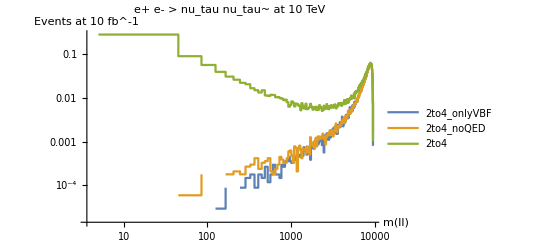

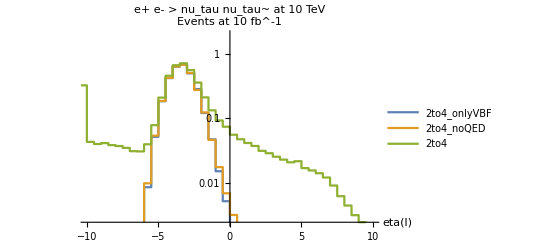

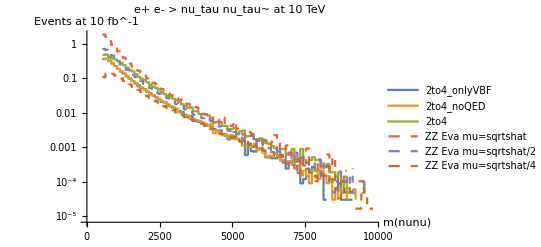

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

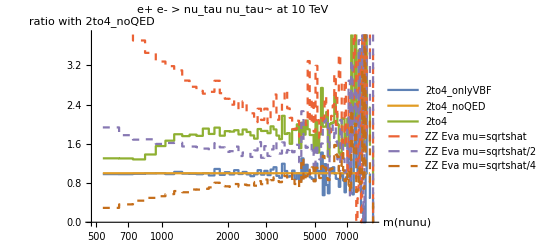

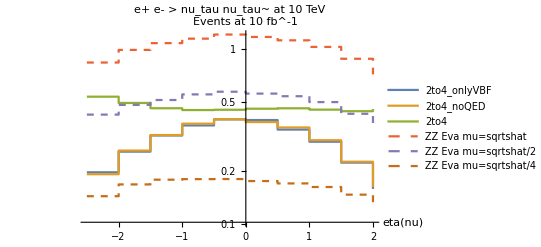

```mathematica
ListLogLogPlot[{joinbin[MllonlyVBF,4],joinbin[MllnoQED,4],joinbin[Mll,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[etalonlyVBF,1],joinbin[etalnoQED,1],joinbin[etal,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotRange->{{-10,10},{0,2}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[MnnonlyVBF,10],joinbin[MnnnoQED,10],joinbin[Mnn,10],joinbin[MnnZZ,10],joinbin[MnnZZmuhalf,10],joinbin[MnnZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","Events at 10 fb^-1"}] 

ListLogLinearPlot[{rapp[joinbin[MnnonlyVBF,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnnoQED,10],joinbin[MnnnoQED,10]],rapp[joinbin[Mnn,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZ,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZmuhalf,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZmuquarter,10],joinbin[MnnnoQED,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","ratio with 2to4_noQED"}] 

ListLogPlot[{etanonlyVBF,etannoQED,etan,etanZZ,etanZZmuhalf,etanZZmuquarter},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(nu)","Events at 10 fb^-1"}]
```

```mathematica
Plus@@Map[#[[2]]&,etan]
Plus@@Map[#[[2]]&,Mll]
Plus@@Map[#[[2]]&,Mnn]
Plus@@Map[#[[2]]&,etanZZ]
```

4.65501

4.65501

4.65501

10.2269

M(nunu)>200 GeV no other cuts

```mathematica
(*namerun="Mnunu300"*)
namerun="Mnunu200"
```

Mnunu200

```mathematica
namefolder="mupem_to_mupemvtatvta_2to4";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etal=prova[5];
Mll =prova[14];
Mnn =prova[15];
etan=prova[10];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_PT},{10_ETA},{11_PT},{12_PT},{13_ETA},{14_M},{15_M},{16_M},{17_M},{18_M},{19_M},{20_DELTAR},{21_DELTAR},{22_MT_MET},{23_MT_MET}}

```mathematica
namefolder="mupem_to_mupemvtatvta_2to4_noQED";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalnoQED=prova[5];
MllnoQED =prova[14];
MnnnoQED =prova[15];
etannoQED=prova[10];

namefolder="mupem_to_mupemvtatvta_2to4_onlyVBFdiagrams";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalonlyVBF=prova[5];
MllonlyVBF =prova[14];
MnnonlyVBF =prova[15];
etanonlyVBF=prova[10];
```

```mathematica
(*namerun="test180"*)
```

```mathematica
namefolder="ZZ_vtatvta_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZ =prova[10];
etanZZ=prova[6];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZmuhalf =prova[10];
etanZZmuhalf=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZmuquarter =prova[10];
etanZZmuquarter=prova[6];


(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZptmu =prova[10];
etanZZptmu=prova[6];*)
```

```mathematica
plotlegend={"2to4_onlyVBF","2to4_noQED","2to4","ZZ Eva mu=sqrtshat","ZZ Eva mu=sqrtshat/2","ZZ Eva mu=sqrtshat/4","ZZ Eva mu=sqrtshat, pt evol"};
plotstyle={Thick,Thick,Thick,Dashed,Dashed,Dashed,Dashed}
```

{Thickness[Large],Thickness[Large],Thickness[Large],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}]}

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="e+ e- > nu_tau nu_tau~ at 10 TeV";
```

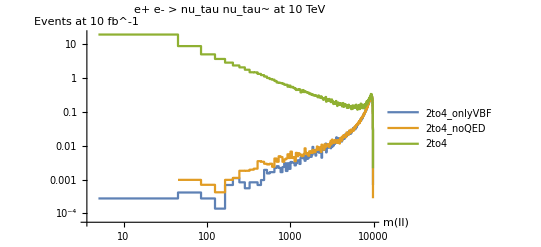

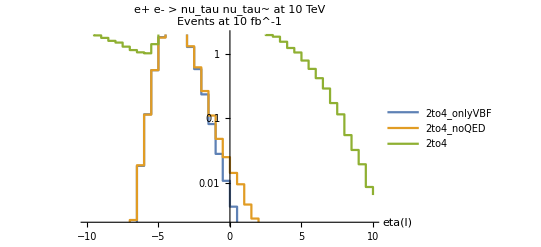

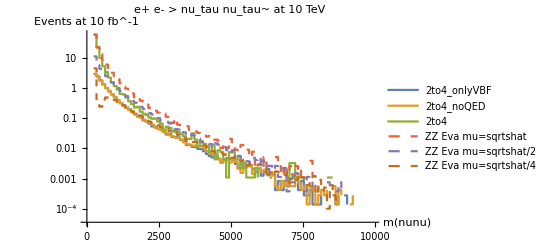

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

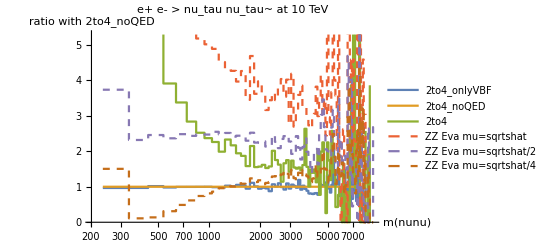

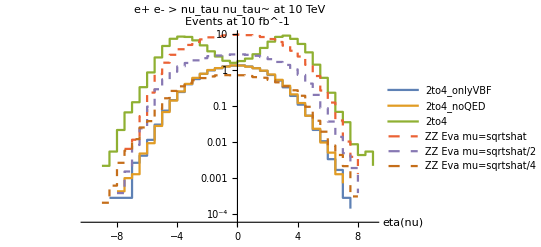

```mathematica
ListLogLogPlot[{joinbin[MllonlyVBF,4],joinbin[MllnoQED,4],joinbin[Mll,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[etalonlyVBF,1],joinbin[etalnoQED,1],joinbin[etal,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotRange->{{-10,10},{0,2}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[MnnonlyVBF,10],joinbin[MnnnoQED,10],joinbin[Mnn,10],joinbin[MnnZZ,10],joinbin[MnnZZmuhalf,10],joinbin[MnnZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","Events at 10 fb^-1"}] 

ListLogLinearPlot[{rapp[joinbin[MnnonlyVBF,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnnoQED,10],joinbin[MnnnoQED,10]],rapp[joinbin[Mnn,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZ,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZmuhalf,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZmuquarter,10],joinbin[MnnnoQED,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","ratio with 2to4_noQED"}] 

ListLogPlot[{etanonlyVBF,etannoQED,etan,etanZZ,etanZZmuhalf,etanZZmuquarter},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(nu)","Events at 10 fb^-1"}]
```

```mathematica
Plus@@Map[#[[2]]&,etan]
Plus@@Map[#[[2]]&,Mll]
Plus@@Map[#[[2]]&,Mnn]
Plus@@Map[#[[2]]&,etanZZ]
```

108.274

108.274

108.274

128.629

M(nunu)>5000 GeV con anche Pt(nu)> 1500 GeV e |eta(nu)|<2.5. Collisioni a 100 TeV

```mathematica
(*namerun="Mnunu300"*)
namerun="Mnunu5000_ptnu1500_eta2half"
suffix="_100TeV"
```

Mnunu5000_ptnu1500_eta2half

_100TeV

```mathematica
namefolder="mupem_to_mupemvtatvta_2to4";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>suffix<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>suffix<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etal=prova[5];
Mll =prova[14];
Mnn =prova[15];
etan=prova[10];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_PT},{10_ETA},{11_PT},{12_PT},{13_ETA},{14_M},{15_M},{16_M},{17_M},{18_M},{19_M},{20_DELTAR},{21_DELTAR},{22_MT_MET},{23_MT_MET}}

```mathematica
namefolder="mupem_to_mupemvtatvta_2to4_noQED";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>suffix<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>suffix<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalnoQED=prova[5];
MllnoQED =prova[14];
MnnnoQED =prova[15];
etannoQED=prova[10];

namefolder="mupem_to_mupemvtatvta_2to4_onlyVBFdiagrams";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>suffix<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>suffix<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalonlyVBF=prova[5];
MllonlyVBF =prova[14];
MnnonlyVBF =prova[15];
etanonlyVBF=prova[10];
```

```mathematica
(*namerun="test180"*)
```

```mathematica
namefolder="ZZ_vtatvta_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>suffix<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>suffix<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZ =prova[10];
etanZZ=prova[6];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>suffix<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>suffix<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZmuhalf =prova[10];
etanZZmuhalf=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>suffix<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>suffix<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZmuquarter =prova[10];
etanZZmuquarter=prova[6];


(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MnnZZptmu =prova[10];
etanZZptmu=prova[6];*)
```

```mathematica
plotlegend={"2to4_onlyVBF","2to4_noQED","2to4","ZZ Eva mu=sqrtshat","ZZ Eva mu=sqrtshat/2","ZZ Eva mu=sqrtshat/4","ZZ Eva mu=sqrtshat, pt evol"};
plotstyle={Thick,Thick,Thick,Dashed,Dashed,Dashed,Dashed}
```

{Thickness[Large],Thickness[Large],Thickness[Large],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}],Dashing[{Small,Small}]}

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="e+ e- > nu_tau nu_tau~ at 10 TeV";
```

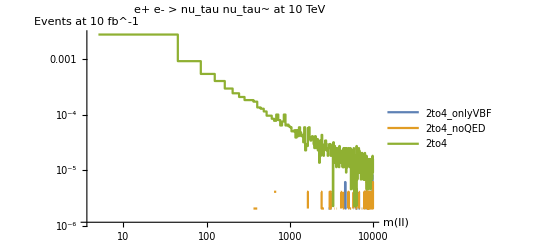

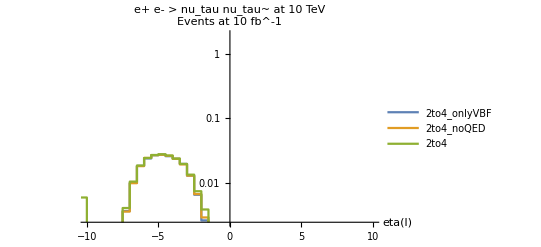

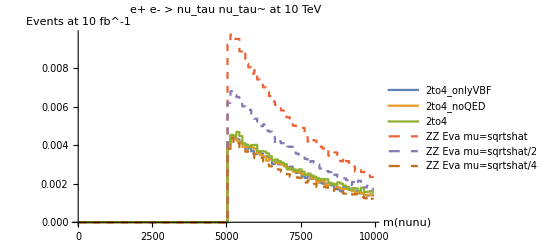

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

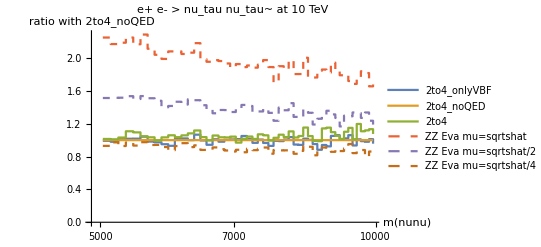

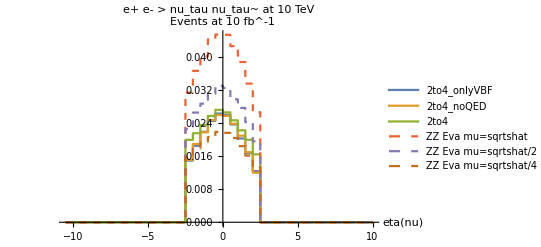

```mathematica
ListLogLogPlot[{joinbin[MllonlyVBF,4],joinbin[MllnoQED,4],joinbin[Mll,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[etalonlyVBF,1],joinbin[etalnoQED,1],joinbin[etal,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotRange->{{-10,10},{0,2}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

ListPlot[{joinbin[MnnonlyVBF,10],joinbin[MnnnoQED,10],joinbin[Mnn,10],joinbin[MnnZZ,10],joinbin[MnnZZmuhalf,10],joinbin[MnnZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","Events at 10 fb^-1"}] 

ListLogLinearPlot[{rapp[joinbin[MnnonlyVBF,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnnoQED,10],joinbin[MnnnoQED,10]],rapp[joinbin[Mnn,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZ,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZmuhalf,10],joinbin[MnnnoQED,10]],rapp[joinbin[MnnZZmuquarter,10],joinbin[MnnnoQED,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(nunu)","ratio with 2to4_noQED"}] 

ListPlot[{etanonlyVBF,etannoQED,etan,etanZZ,etanZZmuhalf,etanZZmuquarter},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(nu)","Events at 10 fb^-1"}]
```

```mathematica
Plus@@Map[#[[2]]&,etan]
Plus@@Map[#[[2]]&,Mll]
Plus@@Map[#[[2]]&,Mnn]
Plus@@Map[#[[2]]&,etanZZ]
```

0.227233

0.227233

0.227233

0.38375